This calculation is for a two plaquette system with periodic boundary conditions and mirroring between the upper and lower links on a matterless lattice. Using Soni and Trivedi’s definition of entanglement entropy, the entanglement entropy is calculated for an SU(3) gauge theory with truncation at the 8-representation.

```mathematica
up:={{1},{0}}
down:={{0},{1}}
s1:=KroneckerProduct[up,up]
s2:=KroneckerProduct[up,down]
s3:=KroneckerProduct[down,up]
s4:=KroneckerProduct[down,down]
s111:=KroneckerProduct[KroneckerProduct[s1,s1],s1]
s13bar1:=KroneckerProduct[KroneckerProduct[s1,s3],s1]
s131:=KroneckerProduct[KroneckerProduct[s1,s2],s1]
s33bar3:=KroneckerProduct[KroneckerProduct[s2,s3],s2]
s3bar33bar:=KroneckerProduct[KroneckerProduct[s3,s2],s3]
s3bar13bar:=KroneckerProduct[KroneckerProduct[s3,s1],s3]
s313:=KroneckerProduct[KroneckerProduct[s2,s1],s2]
s333:=KroneckerProduct[KroneckerProduct[s2,s2],s2]
s3bar3bar3bar:=KroneckerProduct[KroneckerProduct[s3,s3],s3]
s888:=KroneckerProduct[KroneckerProduct[s4,s4],s4]
s181:=KroneckerProduct[KroneckerProduct[s1,s4],s1]
s881:=KroneckerProduct[KroneckerProduct[s4,s4],s1]
s188:=KroneckerProduct[KroneckerProduct[s1,s4],s4]
s13bar8:=KroneckerProduct[KroneckerProduct[s1,s3],s4]
s138:=KroneckerProduct[KroneckerProduct[s1,s2],s4]
s83bar1:=KroneckerProduct[KroneckerProduct[s4,s3],s1]
s831:=KroneckerProduct[KroneckerProduct[s4,s2],s1]
s83bar8:=KroneckerProduct[KroneckerProduct[s4,s3],s4]
s838:=KroneckerProduct[KroneckerProduct[s4,s2],s4]
s33bar3:=KroneckerProduct[KroneckerProduct[s2,s3],s2]
s3bar33bar:=KroneckerProduct[KroneckerProduct[s3,s2],s3]
s3bar83bar:=KroneckerProduct[KroneckerProduct[s3,s4],s3]
s383:=KroneckerProduct[KroneckerProduct[s2,s4],s2]
s818:=KroneckerProduct[KroneckerProduct[s4,s1],s4]
s311:=KroneckerProduct[KroneckerProduct[s2,s1],s1]
s3bar11:=KroneckerProduct[KroneckerProduct[s3,s1],s1]
s133:=KroneckerProduct[KroneckerProduct[s1,s2],s2]
s13bar3bar:=KroneckerProduct[KroneckerProduct[s1,s3],s3]
s33bar3bar:=KroneckerProduct[KroneckerProduct[s2,s3],s3]
s3bar33:=KroneckerProduct[KroneckerProduct[s3,s2],s2]
s811:=KroneckerProduct[KroneckerProduct[s4,s1],s1]
s318:=KroneckerProduct[KroneckerProduct[s2,s1],s4]
s3bar18:=KroneckerProduct[KroneckerProduct[s3,s1],s4]
s381:=KroneckerProduct[KroneckerProduct[s2,s4],s1]
s3bar81:=KroneckerProduct[KroneckerProduct[s3,s4],s1]
s388:=KroneckerProduct[KroneckerProduct[s2,s4],s4]
s3bar88:=KroneckerProduct[KroneckerProduct[s3,s4],s4]
s833:=KroneckerProduct[KroneckerProduct[s4,s2],s2]
s83bar3bar:=KroneckerProduct[KroneckerProduct[s4,s3],s3]
s33bar3bar:=KroneckerProduct[KroneckerProduct[s2,s3],s3]
s3bar33:=KroneckerProduct[KroneckerProduct[s3,s2],s2]
```

```mathematica
Hb8[g_,a_]:=1/(2g^2a^2)*
{{6,0,0,-1,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,6,0,-1,0,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,-1,0,0},
{0,0,6,0,-1,0,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,-1,0},
{-1,-1,0,6,-1,0,0,0,-1,-1,0,0,0,0,-1,0,-1,0,-1,0,0,0,0,0,0},
{-1,0,-1,-1,6,0,0,-1,0,-1,0,0,0,0,0,-1,0,-1,0,-1,0,0,0,0,0},
{-1,-1,0,0,0,6,-1,-1,0,0,0,0,0,0,-1,0,-1,0,-1,0,0,0,0,0,-1},
{-1,0,-1,0,0,-1,6,0,-1,0,0,0,0,0,0,-1,0,-1,0,-1,0,0,0,0,-1},
{0,-1,-1,0,-1,-1,0,6,0,0,0,0,0,0,-1,-1,-1,-1,-1,-1,0,-1,-1,0,0},
{0,-1,-1,-1,0,0,-1,0,6,0,0,0,0,0,-1,-1,-1,-1,-1,-1,-1,0,0,-1,0},
{0,0,0,-1,-1,0,0,0,0,6,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,0},
{0,0,0,0,0,0,0,0,0,0,6,0,0,0,0,0,0,0,0,0,-1,-1,-1,-1,0},
{0,0,0,0,0,0,0,0,0,0,0,6,0,0,0,0,0,0,0,0,-1,-1,-1,-1,0},
{0,0,0,0,0,0,0,0,0,0,0,0,6,0,0,0,0,0,0,0,-1,-1,-1,-1,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,6,0,0,0,0,0,0,-1,-1,-1,-1,0},
{0,0,0,-1,0,-1,0,-1,-1,0,0,0,0,0,6,0,0,0,0,0,-1,0,-1,0,0},
{0,0,0,0,-1,0,-1,-1,-1,0,0,0,0,0,0,6,0,0,0,0,0,-1,0,-1,0},
{0,0,0,-1,0,-1,0,-1,-1,0,0,0,0,0,0,0,6,0,0,0,-1,0,-1,0,0},
{0,0,0,0,-1,0,-1,-1,-1,0,0,0,0,0,0,0,0,6,0,0,0,-1,0,-1,0},
{0,0,0,-1,0,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,6,0,-1,0,-1,0,0},
{0,0,0,0,-1,0,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,6,0,-1,0,-1,0},
{0,-1,0,0,0,0,0,0,-1,0,-1,-1,-1,-1,-1,0,-1,0,-1,0,6,-1,0,0,-1},
{0,0,-1,0,0,0,0,-1,0,0,-1,-1,-1,-1,0,-1,0,-1,0,-1,-1,6,0,0,-1},
{0,-1,0,0,0,0,0,-1,0,-1,-1,-1,-1,-1,-1,0,-1,0,-1,0,0,0,6,-1,0},
{0,0,-1,0,0,0,0,0,-1,-1,-1,-1,-1,-1,0,-1,0,-1,0,-1,0,0,-1,6,0},
{0,0,0,0,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,0,0,6}}
He8[g_]:=g^2/2{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,16/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,16/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,16/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,16/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,16/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,16/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,24/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,24/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,36/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,36/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,45/3,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,45/3,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,54/3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25/3,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,34/3,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,34/3,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,34/3,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,34/3,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,34/3,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,34/3,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,34/3}}
H8[g_,a_]:=Hb8[g,a]+He8[g]+100IdentityMatrix[25]
```

```mathematica
GS8[g_,a_]:=Part[Eigenvectors[H8[g,a]],25]
e1[g_,a_]:=Part[GS8[g,a],1]s111
e2[g_,a_]:=Part[GS8[g,a],2]s13bar1
e3[g_,a_]:=Part[GS8[g,a],3]s131
e4[g_,a_]:=Part[GS8[g,a],4]s33bar3
e5[g_,a_]:=Part[GS8[g,a],5]s3bar33bar
e6[g_,a_]:=Part[GS8[g,a],6]s3bar13bar
e7[g_,a_]:=Part[GS8[g,a],7]s313
e8[g_,a_]:=Part[GS8[g,a],8]s333
e9[g_,a_]:=Part[GS8[g,a],9]s3bar3bar3bar
e10[g_,a_]:=Part[GS8[g,a],10]s888
e11[g_,a_]:=Part[GS8[g,a],11]s181
e12[g_,a_]:=Part[GS8[g,a],12]s881
e13[g_,a_]:=Part[GS8[g,a],13]s188
e14[g_,a_]:=Part[GS8[g,a],14]s888
e15[g_,a_]:=Part[GS8[g,a],15]s13bar8
e16[g_,a_]:=Part[GS8[g,a],16]s138
e17[g_,a_]:=Part[GS8[g,a],17]s83bar1
e18[g_,a_]:=Part[GS8[g,a],18]s831
e19[g_,a_]:=Part[GS8[g,a],19]s83bar8
e20[g_,a_]:=Part[GS8[g,a],20]s838
e21[g_,a_]:=Part[GS8[g,a],21]s33bar3
e22[g_,a_]:=Part[GS8[g,a],22]s3bar33bar
e23[g_,a_]:=Part[GS8[g,a],23]s3bar83bar
e24[g_,a_]:=Part[GS8[g,a],24]s383
e25[g_,a_]:=Part[GS8[g,a],25]s818
```

```mathematica
RDM8A[g_,a_]:=e1[g,a].Transpose[e1[g,a]]+e1[g,a].Transpose[e4[g,a]]+e1[g,a].Transpose[e5[g,a]]+e1[g,a].Transpose[e10[g,a]]+
e2[g,a].Transpose[e2[g,a]]+e2[g,a].Transpose[e6[g,a]]+e2[g,a].Transpose[e8[g,a]]+e2[g,a].Transpose[e15[g,a]]+e2[g,a].Transpose[e17[g,a]]+e2[g,a].Transpose[e19[g,a]]+e2[g,a].Transpose[e23[g,a]]+
e3[g,a].Transpose[e3[g,a]]+e3[g,a].Transpose[e7[g,a]]+e3[g,a].Transpose[e9[g,a]]+e3[g,a].Transpose[e16[g,a]]+e3[g,a].Transpose[e18[g,a]]+e3[g,a].Transpose[e20[g,a]]+e3[g,a].Transpose[e24[g,a]]+
e4[g,a].Transpose[e1[g,a]]+e4[g,a].Transpose[e4[g,a]]+e4[g,a].Transpose[e5[g,a]]+e4[g,a].Transpose[e10[g,a]]+
e5[g,a].Transpose[e1[g,a]]+e5[g,a].Transpose[e4[g,a]]+e5[g,a].Transpose[e5[g,a]]+e5[g,a].Transpose[e10[g,a]]+
e6[g,a].Transpose[e2[g,a]]+e6[g,a].Transpose[e6[g,a]]+e6[g,a].Transpose[e8[g,a]]+e6[g,a].Transpose[e15[g,a]]+e6[g,a].Transpose[e17[g,a]]+e6[g,a].Transpose[e19[g,a]]+e6[g,a].Transpose[e23[g,a]]+
e7[g,a].Transpose[e3[g,a]]+e7[g,a].Transpose[e7[g,a]]+e7[g,a].Transpose[e9[g,a]]+e7[g,a].Transpose[e16[g,a]]+e7[g,a].Transpose[e18[g,a]]+e7[g,a].Transpose[e20[g,a]]+e7[g,a].Transpose[e24[g,a]]+
e8[g,a].Transpose[e2[g,a]]+e8[g,a].Transpose[e6[g,a]]+e8[g,a].Transpose[e8[g,a]]+e8[g,a].Transpose[e15[g,a]]+e8[g,a].Transpose[e17[g,a]]+e8[g,a].Transpose[e19[g,a]]+e8[g,a].Transpose[e23[g,a]]+
e9[g,a].Transpose[e3[g,a]]+e9[g,a].Transpose[e7[g,a]]+e9[g,a].Transpose[e9[g,a]]+e9[g,a].Transpose[e16[g,a]]+e9[g,a].Transpose[e18[g,a]]+e9[g,a].Transpose[e20[g,a]]+e9[g,a].Transpose[e24[g,a]]+
e10[g,a].Transpose[e1[g,a]]+e10[g,a].Transpose[e4[g,a]]+e10[g,a].Transpose[e5[g,a]]+e10[g,a].Transpose[e10[g,a]]+
e11[g,a].Transpose[e11[g,a]]+e11[g,a].Transpose[e12[g,a]]+e11[g,a].Transpose[e13[g,a]]+e11[g,a].Transpose[e14[g,a]]+e11[g,a].Transpose[e21[g,a]]+e11[g,a].Transpose[e22[g,a]]+e11[g,a].Transpose[e25[g,a]]+
e12[g,a].Transpose[e11[g,a]]+e12[g,a].Transpose[e12[g,a]]+e12[g,a].Transpose[e13[g,a]]+e12[g,a].Transpose[e14[g,a]]+e12[g,a].Transpose[e21[g,a]]+e12[g,a].Transpose[e22[g,a]]+e12[g,a].Transpose[e25[g,a]]+
e13[g,a].Transpose[e11[g,a]]+e13[g,a].Transpose[e12[g,a]]+e13[g,a].Transpose[e13[g,a]]+e13[g,a].Transpose[e14[g,a]]+e13[g,a].Transpose[e21[g,a]]+e13[g,a].Transpose[e22[g,a]]+e13[g,a].Transpose[e25[g,a]]+
e14[g,a].Transpose[e11[g,a]]+e14[g,a].Transpose[e12[g,a]]+e14[g,a].Transpose[e13[g,a]]+e14[g,a].Transpose[e14[g,a]]+e14[g,a].Transpose[e21[g,a]]+e14[g,a].Transpose[e22[g,a]]+e14[g,a].Transpose[e25[g,a]]+
e15[g,a].Transpose[e2[g,a]]+e15[g,a].Transpose[e6[g,a]]+e15[g,a].Transpose[e8[g,a]]+e15[g,a].Transpose[e15[g,a]]+e15[g,a].Transpose[e17[g,a]]+e15[g,a].Transpose[e19[g,a]]+e15[g,a].Transpose[e23[g,a]]+
e16[g,a].Transpose[e3[g,a]]+e16[g,a].Transpose[e7[g,a]]+e16[g,a].Transpose[e9[g,a]]+e16[g,a].Transpose[e16[g,a]]+e16[g,a].Transpose[e18[g,a]]+e16[g,a].Transpose[e20[g,a]]+e16[g,a].Transpose[e24[g,a]]+
e17[g,a].Transpose[e2[g,a]]+e17[g,a].Transpose[e6[g,a]]+e17[g,a].Transpose[e8[g,a]]+e17[g,a].Transpose[e15[g,a]]+e17[g,a].Transpose[e17[g,a]]+e17[g,a].Transpose[e19[g,a]]+e17[g,a].Transpose[e23[g,a]]+
e18[g,a].Transpose[e3[g,a]]+e18[g,a].Transpose[e7[g,a]]+e18[g,a].Transpose[e9[g,a]]+e18[g,a].Transpose[e16[g,a]]+e18[g,a].Transpose[e18[g,a]]+e18[g,a].Transpose[e20[g,a]]+e18[g,a].Transpose[e24[g,a]]+
e19[g,a].Transpose[e2[g,a]]+e19[g,a].Transpose[e6[g,a]]+e19[g,a].Transpose[e8[g,a]]+e19[g,a].Transpose[e15[g,a]]+e19[g,a].Transpose[e17[g,a]]+e19[g,a].Transpose[e19[g,a]]+e19[g,a].Transpose[e23[g,a]]+
e20[g,a].Transpose[e3[g,a]]+e20[g,a].Transpose[e7[g,a]]+e20[g,a].Transpose[e9[g,a]]+e20[g,a].Transpose[e16[g,a]]+e20[g,a].Transpose[e18[g,a]]+e20[g,a].Transpose[e20[g,a]]+e20[g,a].Transpose[e24[g,a]]+
e21[g,a].Transpose[e11[g,a]]+e21[g,a].Transpose[e12[g,a]]+e21[g,a].Transpose[e13[g,a]]+e21[g,a].Transpose[e14[g,a]]+e21[g,a].Transpose[e21[g,a]]+e21[g,a].Transpose[e22[g,a]]+e21[g,a].Transpose[e25[g,a]]+
e22[g,a].Transpose[e11[g,a]]+e22[g,a].Transpose[e12[g,a]]+e22[g,a].Transpose[e13[g,a]]+e22[g,a].Transpose[e14[g,a]]+e22[g,a].Transpose[e21[g,a]]+e22[g,a].Transpose[e22[g,a]]+e22[g,a].Transpose[e25[g,a]]+
e23[g,a].Transpose[e2[g,a]]+e23[g,a].Transpose[e6[g,a]]+e23[g,a].Transpose[e8[g,a]]+e23[g,a].Transpose[e15[g,a]]+e23[g,a].Transpose[e17[g,a]]+e23[g,a].Transpose[e19[g,a]]+e23[g,a].Transpose[e23[g,a]]+
e24[g,a].Transpose[e3[g,a]]+e24[g,a].Transpose[e7[g,a]]+e24[g,a].Transpose[e9[g,a]]+e24[g,a].Transpose[e16[g,a]]+e24[g,a].Transpose[e18[g,a]]+e24[g,a].Transpose[e20[g,a]]+e24[g,a].Transpose[e24[g,a]]+
e25[g,a].Transpose[e11[g,a]]+e25[g,a].Transpose[e12[g,a]]+e25[g,a].Transpose[e13[g,a]]+e25[g,a].Transpose[e14[g,a]]+e25[g,a].Transpose[e21[g,a]]+e25[g,a].Transpose[e22[g,a]]+e25[g,a].Transpose[e25[g,a]]
```

```mathematica
S8A[g_,a_]:=-Part[Eigenvalues[RDM8A[g,a]],1]Log[2,Part[Eigenvalues[RDM8A[g,a]],1]]-Part[Eigenvalues[RDM8A[g,a]],2]Log[2,Part[Eigenvalues[RDM8A[g,a]],2]]-Part[Eigenvalues[RDM8A[g,a]],3]Log[2,Part[Eigenvalues[RDM8A[g,a]],3]]-Part[Eigenvalues[RDM8A[g,a]],4]Log[2,Part[Eigenvalues[RDM8A[g,a]],4]]
```

```mathematica
t1[g_,a_]:=Part[GS8[g,a],1]s111
t2[g_,a_]:=Part[GS8[g,a],2]s311
t3[g_,a_]:=Part[GS8[g,a],3]s3bar11
t4[g_,a_]:=Part[GS8[g,a],4]s133
t5[g_,a_]:=Part[GS8[g,a],5]s13bar3bar
t6[g_,a_]:=Part[GS8[g,a],6]s33bar3bar
t7[g_,a_]:=Part[GS8[g,a],7]s3bar33
t8[g_,a_]:=Part[GS8[g,a],8]s333
t9[g_,a_]:=Part[GS8[g,a],9]s3bar3bar3bar
t10[g_,a_]:=Part[GS8[g,a],10]s188
t11[g_,a_]:=Part[GS8[g,a],11]s811
t12[g_,a_]:=Part[GS8[g,a],12]s881
t13[g_,a_]:=Part[GS8[g,a],13]s818
t14[g_,a_]:=Part[GS8[g,a],14]s888
t15[g_,a_]:=Part[GS8[g,a],15]s318
t16[g_,a_]:=Part[GS8[g,a],16]s3bar18
t17[g_,a_]:=Part[GS8[g,a],17]s381
t18[g_,a_]:=Part[GS8[g,a],18]s3bar81
t19[g_,a_]:=Part[GS8[g,a],19]s388
t20[g_,a_]:=Part[GS8[g,a],20]s3bar88
t21[g_,a_]:=Part[GS8[g,a],21]s833
t22[g_,a_]:=Part[GS8[g,a],22]s83bar3bar
t23[g_,a_]:=Part[GS8[g,a],23]s33bar3bar
t24[g_,a_]:=Part[GS8[g,a],24]s3bar33
t25[g_,a_]:=Part[GS8[g,a],25]s888
```

```mathematica
RDM8B[g_,a_]:=t1[g,a].Transpose[t1[g,a]]+t1[g,a].Transpose[t6[g,a]]+t1[g,a].Transpose[t7[g,a]]+t1[g,a].Transpose[t25[g,a]]+
t2[g,a].Transpose[t2[g,a]]+t2[g,a].Transpose[t4[g,a]]+t2[g,a].Transpose[t9[g,a]]+t2[g,a].Transpose[t15[g,a]]+t2[g,a].Transpose[t17[g,a]]+t2[g,a].Transpose[t19[g,a]]+t2[g,a].Transpose[t21[g,a]]+
t3[g,a].Transpose[t3[g,a]]+t3[g,a].Transpose[t5[g,a]]+t3[g,a].Transpose[t8[g,a]]+t3[g,a].Transpose[t16[g,a]]+t3[g,a].Transpose[t18[g,a]]+t3[g,a].Transpose[t20[g,a]]+t3[g,a].Transpose[t22[g,a]]+
t4[g,a].Transpose[t2[g,a]]+t4[g,a].Transpose[t4[g,a]]+t4[g,a].Transpose[t9[g,a]]+t4[g,a].Transpose[t15[g,a]]+t4[g,a].Transpose[t17[g,a]]+t4[g,a].Transpose[t19[g,a]]+t4[g,a].Transpose[t21[g,a]]+
t5[g,a].Transpose[t3[g,a]]+t5[g,a].Transpose[t5[g,a]]+t5[g,a].Transpose[t8[g,a]]+t5[g,a].Transpose[t16[g,a]]+t5[g,a].Transpose[t18[g,a]]+t5[g,a].Transpose[t20[g,a]]+t5[g,a].Transpose[t22[g,a]]+
t6[g,a].Transpose[t1[g,a]]+t6[g,a].Transpose[t6[g,a]]+t6[g,a].Transpose[t7[g,a]]+t6[g,a].Transpose[t25[g,a]]+
t7[g,a].Transpose[t1[g,a]]+t7[g,a].Transpose[t6[g,a]]+t7[g,a].Transpose[t7[g,a]]+t7[g,a].Transpose[t25[g,a]]+
t8[g,a].Transpose[t3[g,a]]+t8[g,a].Transpose[t5[g,a]]+t8[g,a].Transpose[t8[g,a]]+t8[g,a].Transpose[t16[g,a]]+t8[g,a].Transpose[t18[g,a]]+t8[g,a].Transpose[t20[g,a]]+t8[g,a].Transpose[t22[g,a]]+
t9[g,a].Transpose[t2[g,a]]+t9[g,a].Transpose[t4[g,a]]+t9[g,a].Transpose[t9[g,a]]+t9[g,a].Transpose[t15[g,a]]+t9[g,a].Transpose[t17[g,a]]+t9[g,a].Transpose[t19[g,a]]+t9[g,a].Transpose[t21[g,a]]+
t10[g,a].Transpose[t10[g,a]]+t10[g,a].Transpose[t11[g,a]]+t10[g,a].Transpose[t12[g,a]]+t10[g,a].Transpose[t13[g,a]]+t10[g,a].Transpose[t14[g,a]]+t10[g,a].Transpose[t23[g,a]]+t10[g,a].Transpose[t24[g,a]]+
t11[g,a].Transpose[t10[g,a]]+t11[g,a].Transpose[t11[g,a]]+t11[g,a].Transpose[t12[g,a]]+t11[g,a].Transpose[t13[g,a]]+t11[g,a].Transpose[t14[g,a]]+t11[g,a].Transpose[t23[g,a]]+t11[g,a].Transpose[t24[g,a]]+
t12[g,a].Transpose[t10[g,a]]+t12[g,a].Transpose[t11[g,a]]+t12[g,a].Transpose[t12[g,a]]+t12[g,a].Transpose[t13[g,a]]+t12[g,a].Transpose[t14[g,a]]+t12[g,a].Transpose[t23[g,a]]+t12[g,a].Transpose[t24[g,a]]+
t13[g,a].Transpose[t10[g,a]]+t13[g,a].Transpose[t11[g,a]]+t13[g,a].Transpose[t12[g,a]]+t13[g,a].Transpose[t13[g,a]]+t13[g,a].Transpose[t14[g,a]]+t13[g,a].Transpose[t23[g,a]]+t13[g,a].Transpose[t24[g,a]]+
t14[g,a].Transpose[t10[g,a]]+t14[g,a].Transpose[t11[g,a]]+t14[g,a].Transpose[t12[g,a]]+t14[g,a].Transpose[t13[g,a]]+t14[g,a].Transpose[t14[g,a]]+t14[g,a].Transpose[t23[g,a]]+t14[g,a].Transpose[t24[g,a]]+
t15[g,a].Transpose[t2[g,a]]+t15[g,a].Transpose[t4[g,a]]+t15[g,a].Transpose[t9[g,a]]+t15[g,a].Transpose[t15[g,a]]+t15[g,a].Transpose[t17[g,a]]+t15[g,a].Transpose[t19[g,a]]+t15[g,a].Transpose[t21[g,a]]+
t16[g,a].Transpose[t3[g,a]]+t16[g,a].Transpose[t5[g,a]]+t16[g,a].Transpose[t8[g,a]]+t16[g,a].Transpose[t16[g,a]]+t16[g,a].Transpose[t18[g,a]]+t16[g,a].Transpose[t20[g,a]]+t16[g,a].Transpose[t22[g,a]]+
t17[g,a].Transpose[t2[g,a]]+t17[g,a].Transpose[t4[g,a]]+t17[g,a].Transpose[t9[g,a]]+t17[g,a].Transpose[t15[g,a]]+t17[g,a].Transpose[t17[g,a]]+t17[g,a].Transpose[t19[g,a]]+t17[g,a].Transpose[t21[g,a]]+
t18[g,a].Transpose[t3[g,a]]+t18[g,a].Transpose[t5[g,a]]+t18[g,a].Transpose[t8[g,a]]+t18[g,a].Transpose[t16[g,a]]+t18[g,a].Transpose[t18[g,a]]+t18[g,a].Transpose[t20[g,a]]+t18[g,a].Transpose[t22[g,a]]+
t19[g,a].Transpose[t2[g,a]]+t19[g,a].Transpose[t4[g,a]]+t19[g,a].Transpose[t9[g,a]]+t19[g,a].Transpose[t15[g,a]]+t19[g,a].Transpose[t17[g,a]]+t19[g,a].Transpose[t19[g,a]]+t19[g,a].Transpose[t21[g,a]]+
t20[g,a].Transpose[t3[g,a]]+t20[g,a].Transpose[t5[g,a]]+t20[g,a].Transpose[t8[g,a]]+t20[g,a].Transpose[t16[g,a]]+t20[g,a].Transpose[t18[g,a]]+t20[g,a].Transpose[t20[g,a]]+t20[g,a].Transpose[t22[g,a]]+
t21[g,a].Transpose[t2[g,a]]+t21[g,a].Transpose[t4[g,a]]+t21[g,a].Transpose[t9[g,a]]+t21[g,a].Transpose[t15[g,a]]+t21[g,a].Transpose[t17[g,a]]+t21[g,a].Transpose[t19[g,a]]+t21[g,a].Transpose[t21[g,a]]+
t22[g,a].Transpose[t3[g,a]]+t22[g,a].Transpose[t5[g,a]]+t22[g,a].Transpose[t8[g,a]]+t22[g,a].Transpose[t16[g,a]]+t22[g,a].Transpose[t18[g,a]]+t22[g,a].Transpose[t20[g,a]]+t22[g,a].Transpose[t22[g,a]]+
t23[g,a].Transpose[t10[g,a]]+t23[g,a].Transpose[t11[g,a]]+t23[g,a].Transpose[t12[g,a]]+t23[g,a].Transpose[t13[g,a]]+t23[g,a].Transpose[t14[g,a]]+t23[g,a].Transpose[t23[g,a]]+t23[g,a].Transpose[t24[g,a]]+
t24[g,a].Transpose[t10[g,a]]+t24[g,a].Transpose[t11[g,a]]+t24[g,a].Transpose[t12[g,a]]+t24[g,a].Transpose[t13[g,a]]+t24[g,a].Transpose[t14[g,a]]+t24[g,a].Transpose[t23[g,a]]+t24[g,a].Transpose[t24[g,a]]+
t25[g,a].Transpose[t1[g,a]]+t25[g,a].Transpose[t6[g,a]]+t25[g,a].Transpose[t7[g,a]]+t25[g,a].Transpose[t25[g,a]]
```

```mathematica
S8B[g_,a_]:=-Part[Eigenvalues[RDM8B[g,a]],1]Log[2,Part[Eigenvalues[RDM8B[g,a]],1]]-Part[Eigenvalues[RDM8B[g,a]],2]Log[2,Part[Eigenvalues[RDM8B[g,a]],2]]-Part[Eigenvalues[RDM8B[g,a]],3]Log[2,Part[Eigenvalues[RDM8B[g,a]],3]]-Part[Eigenvalues[RDM8B[g,a]],4]Log[2,Part[Eigenvalues[RDM8B[g,a]],4]]
```

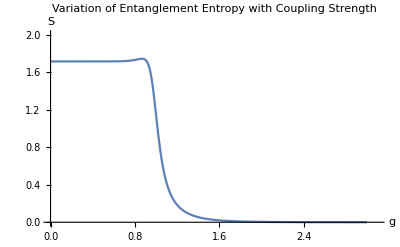

```mathematica
Plot[S8A[g,1],{g,Sqrt[0.00001],3},AxesLabel->{"g","S"},PlotLabel->"Variation of Entanglement Entropy with Coupling Strength",PlotRange->{{0,3.1},{0,2}}]
```

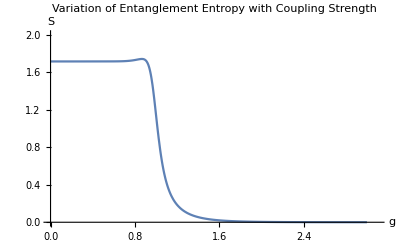

```mathematica
Plot[S8B[g,1],{g,Sqrt[0.00001],3},AxesLabel->{"g","S"},PlotLabel->"Variation of Entanglement Entropy with Coupling Strength",PlotRange->{{0,3.1},{0,2}}]
```

```mathematica
S8A[0.8,1]
S8B[0.8,1]
```

1.72972

1.72848

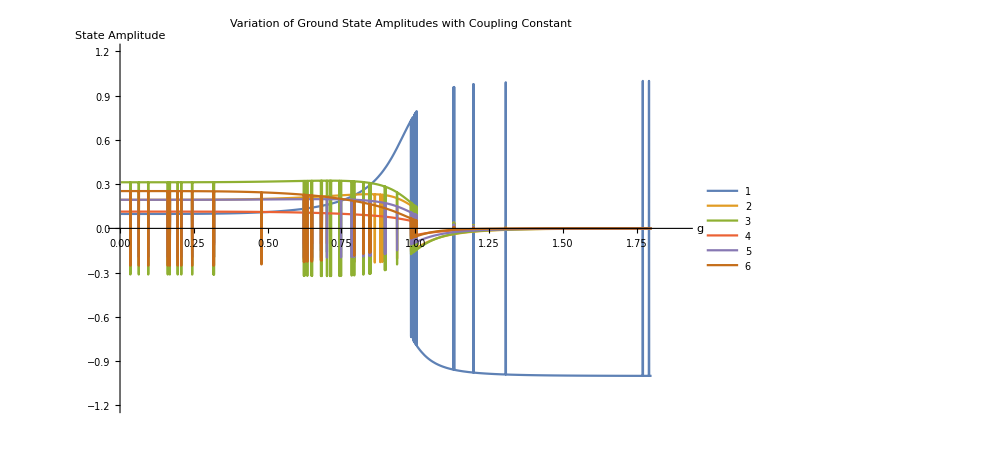

```mathematica
Plot[{Part[GS8[g,1],1],Part[GS8[g,1],2],Part[GS8[g,1],8],Part[GS8[g,1],10],Part[GS8[g,1],15],Part[GS8[g,1],24]},{g,Sqrt[0.00001],1.8},PlotRange->{{0,1.9},{-1.2,1.2}},AxesLabel->{"g","State Amplitude"},PlotLabel->"Variation of Ground State Amplitudes with Coupling Constant",PlotLegends->LineLegend[Automatic]]
```

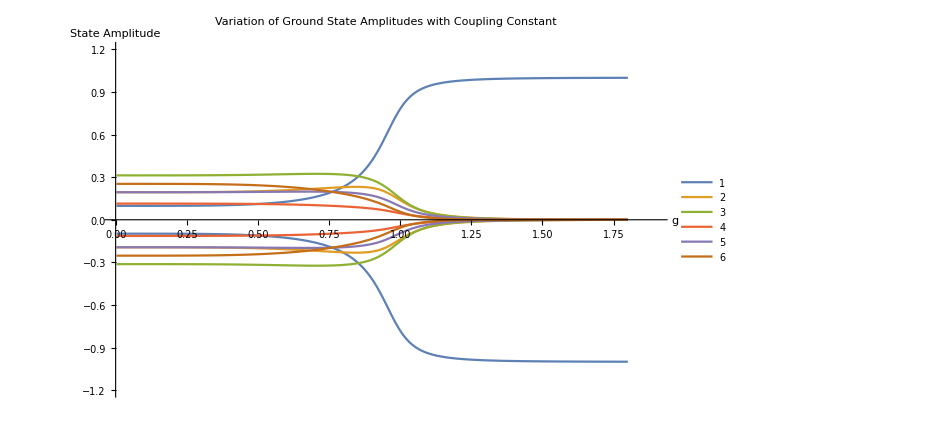

```mathematica
Plot[{Abs[Part[GS8[g,1],1]],Abs[Part[GS8[g,1],2]],Abs[Part[GS8[g,1],8]],Abs[Part[GS8[g,1],10]],Abs[Part[GS8[g,1],15]],Abs[Part[GS8[g,1],24]],-Abs[Part[GS8[g,1],1]],-Abs[Part[GS8[g,1],2]],-Abs[Part[GS8[g,1],8]],-Abs[Part[GS8[g,1],10]],-Abs[Part[GS8[g,1],15]],-Abs[Part[GS8[g,1],24]]},{g,Sqrt[0.00001],1.8},PlotRange->{{0,1.9},{-1.2,1.2}},AxesLabel->{"g","State Amplitude"},PlotLabel->"Variation of Ground State Amplitudes with Coupling Constant",PlotLegends->LineLegend[Automatic],PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5],ColorData[97][6],ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5],ColorData[97][6]}]
```

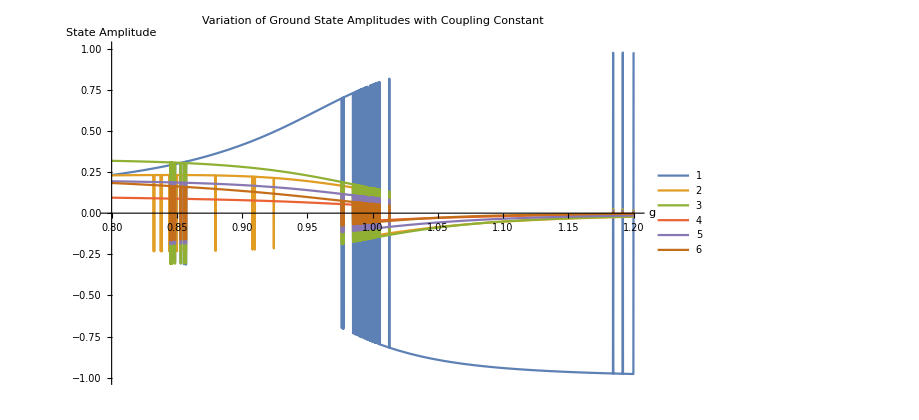

```mathematica
Plot[{Part[GS8[g,1],1],Part[GS8[g,1],2],Part[GS8[g,1],8],Part[GS8[g,1],10],Part[GS8[g,1],15],Part[GS8[g,1],24]},{g,0.8,1.2},PlotRange->{{0.8,1.2},{-1,1}},AxesLabel->{"g","State Amplitude"},PlotLabel->"Variation of Ground State Amplitudes with Coupling Constant",PlotLegends->LineLegend[Automatic]]
```

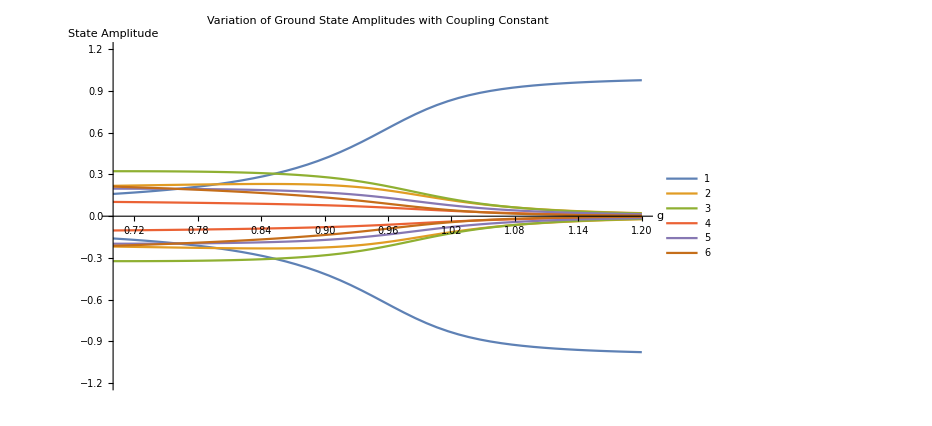

```mathematica
Plot[{Abs[Part[GS8[g,1],1]],Abs[Part[GS8[g,1],2]],Abs[Part[GS8[g,1],8]],Abs[Part[GS8[g,1],10]],Abs[Part[GS8[g,1],15]],Abs[Part[GS8[g,1],24]],-Abs[Part[GS8[g,1],1]],-Abs[Part[GS8[g,1],2]],-Abs[Part[GS8[g,1],8]],-Abs[Part[GS8[g,1],10]],-Abs[Part[GS8[g,1],15]],-Abs[Part[GS8[g,1],24]]},{g,0.7,1.2},PlotRange->{{0.7,1.2},{-1.2,1.2}},AxesLabel->{"g","State Amplitude"},PlotLabel->"Variation of Ground State Amplitudes with Coupling Constant",PlotLegends->LineLegend[Automatic],PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5],ColorData[97][6],ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5],ColorData[97][6]}]
```

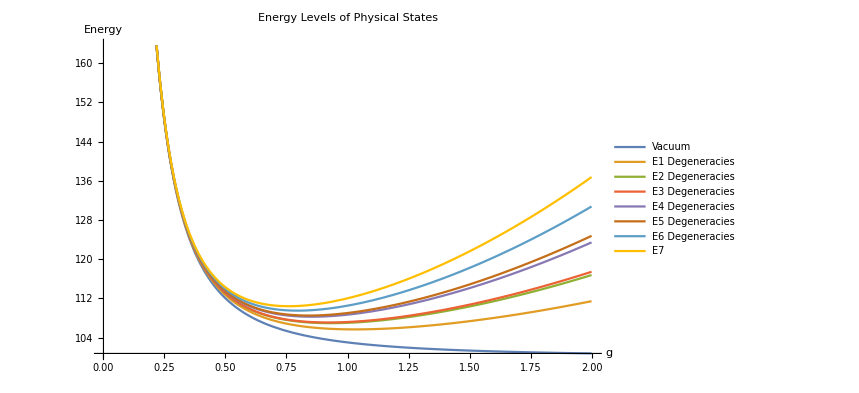

```mathematica
Plot[{Part[Part[H8[g,1],1],1],Part[Part[H8[g,1],2],2],Part[Part[H8[g,1],8],8],Part[Part[H8[g,1],15],15],Part[Part[H8[g,1],19],19],Part[Part[H8[g,1],10],10],Part[Part[H8[g,1],12],12],Part[Part[H8[g,1],14],14]},{g,Sqrt[0.00001],2},PlotLabel->"Energy Levels of Physical States",AxesLabel->{"g","Energy"},PlotLegends->LineLegend[{"Vacuum","E1 Degeneracies", "E2 Degeneracies", "E3 Degeneracies", "E4 Degeneracies", "E5 Degeneracies", "E6 Degeneracies", "E7"}]]
```

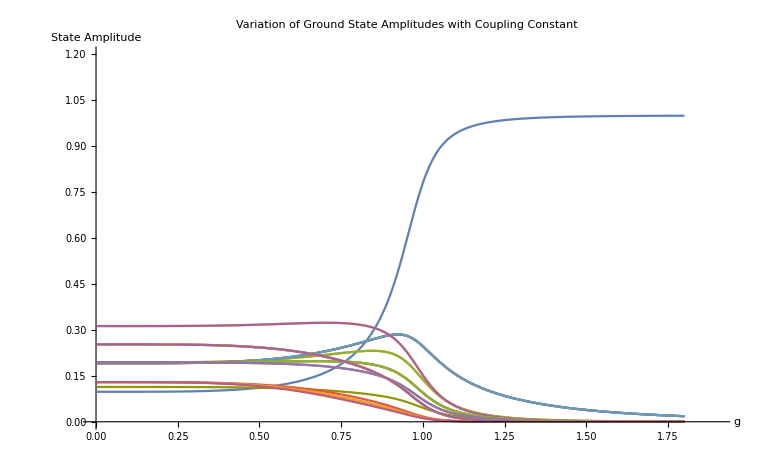

```mathematica
Plot[{Abs[Part[GS8[g,1],1]],Abs[Part[GS8[g,1],2]],Abs[Part[GS8[g,1],3]],Abs[Part[GS8[g,1],4]],Abs[Part[GS8[g,1],5]],Abs[Part[GS8[g,1],6]],Abs[Part[GS8[g,1],7]],Abs[Part[GS8[g,1],8]],Abs[Part[GS8[g,1],9]],Abs[Part[GS8[g,1],10]],Abs[Part[GS8[g,1],11]],Abs[Part[GS8[g,1],12]],Abs[Part[GS8[g,1],13]],Abs[Part[GS8[g,1],14]],Abs[Part[GS8[g,1],15]],Abs[Part[GS8[g,1],16]],Abs[Part[GS8[g,1],17]],Abs[Part[GS8[g,1],18]],Abs[Part[GS8[g,1],19]],Abs[Part[GS8[g,1],20]],Abs[Part[GS8[g,1],21]],Abs[Part[GS8[g,1],22]],Abs[Part[GS8[g,1],23]],Abs[Part[GS8[g,1],24]]},{g,Sqrt[0.00001],1.8},PlotRange->{{0,1.9},{0,1.2}},AxesLabel->{"g","State Amplitude"},PlotLabel->"Variation of Ground State Amplitudes with Coupling Constant"]
```

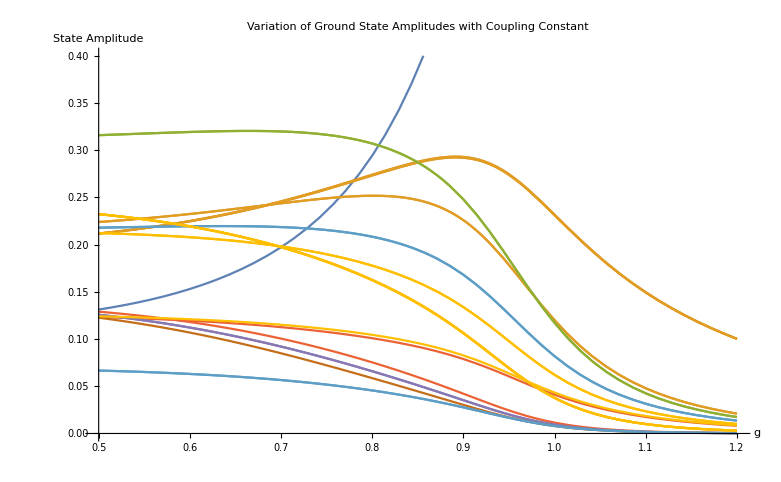

```mathematica
Plot[{Abs[Part[GS8[g,1],1]],Abs[Part[GS8[g,1],2]],Abs[Part[GS8[g,1],3]],Abs[Part[GS8[g,1],4]],Abs[Part[GS8[g,1],5]],Abs[Part[GS8[g,1],6]],Abs[Part[GS8[g,1],7]],Abs[Part[GS8[g,1],8]],Abs[Part[GS8[g,1],9]],Abs[Part[GS8[g,1],10]],Abs[Part[GS8[g,1],11]],Abs[Part[GS8[g,1],12]],Abs[Part[GS8[g,1],13]],Abs[Part[GS8[g,1],14]],Abs[Part[GS8[g,1],15]],Abs[Part[GS8[g,1],16]],Abs[Part[GS8[g,1],17]],Abs[Part[GS8[g,1],18]],Abs[Part[GS8[g,1],19]],Abs[Part[GS8[g,1],20]],Abs[Part[GS8[g,1],21]],Abs[Part[GS8[g,1],22]],Abs[Part[GS8[g,1],23]],Abs[Part[GS8[g,1],24]],Abs[Part[GS8[g,1],25]]},{g,0.5,1.2},PlotRange->{{0.5,1.2},{0,0.4}},AxesLabel->{"g","State Amplitude"},PlotLabel->"Variation of Ground State Amplitudes with Coupling Constant",PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][2],ColorData[97][2],ColorData[97][2],ColorData[97][2],ColorData[97][2],ColorData[97][3],ColorData[97][3],ColorData[97][4],ColorData[97][4],ColorData[97][5],ColorData[97][5],ColorData[97][6],ColorData[97][7],ColorData[97][7],ColorData[97][7],ColorData[97][7],ColorData[97][8],ColorData[97][8],ColorData[97][8],ColorData[97][8],ColorData[97][8],ColorData[97][8],ColorData[97][8]}]
```

```mathematica
2Hb8[1,1]//MatrixForm
```

(6 | 0 | 0 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 0 | -1 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0
0 | 0 | 6 | 0 | -1 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0
-1 | -1 | 0 | 6 | -1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | -1 | -1 | 6 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0
-1 | -1 | 0 | 0 | 0 | 6 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1
-1 | 0 | -1 | 0 | 0 | -1 | 6 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1
0 | -1 | -1 | 0 | -1 | -1 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | 0 | -1 | -1 | 0 | 0
0 | -1 | -1 | -1 | 0 | 0 | -1 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 0 | 0 | -1 | 0
0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | 0
0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0
0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | -1 | 0 | -1 | 0
0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | -1 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | -1 | 0 | -1 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | -1 | -1 | -1 | 0 | -1 | 0 | -1 | 0 | 6 | -1 | 0 | 0 | -1
0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | -1 | 0 | -1 | 0 | -1 | 0 | -1 | -1 | 6 | 0 | 0 | -1
0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 6 | -1 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | 6 | 0
0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 6)